# Using the SACNA package - reverse APED model

The purpose of this document is to give a short tutorial for the SACNA package. 
Let’s start by bringing the package functions to this notebook.

```mathematica
Quiet[ClearAll["Global`*"]];
 Quiet[Remove["Global`*"]];
SetDirectory[NotebookDirectory[]];

Quiet[Get["../SACNA.wl"]]
```

Now let’s input the reactions and rates lists of this model. If we input the rates list as an empty list, SACNA will assign rates by default in the order of the list (the first reaction has constant k1 and so on). Reactions must be in terms of D-species, L-species, Z-species (achiral species), and the empty specie N1.

```mathematica
reactions = {"L1->L2","L2->L1","L2+L1->L3","L3->L2+L1","D2+L1->D4","D4->D2+L1","L3->2L1","2L1->L3","L4->L1+D1","L1+D1->L4","L4->D3","D3->L4"};
rates={};
```

Note that we are not writing all the reactions, only it is left the dual reactions. If we use the function ClausuraDual, we can get all the reactions. This is done by default in the RunSemiAlgebraicAnalysis function.

```mathematica
Quiet[ClausuraDual[reactions]]
```

{L1->L2,L2->L1,L1+L2->L3,L3->L1+L2,D2+L1->D4,D4->D2+L1,L3->2L1,2L1->L3,L4->D1+L1,D1+L1->L4,L4->D3,D3->L4,D1->D2,D2->D1,D1+D2->D3,D3->D1+D2,D1+L2->L4,L4->D1+L2,D3->2D1,2D1->D3,D4->D1+L1,D1+L1->D4,D4->L3,L3->D4}

Now we can run the semialgebraic analysis of the model by using the RunSemiAlgebraicAnalysis function. The first parameter corresponds to the reactions’ list, the second parameter corresponds to the rates’ list, and the last parameter corresponds to time in seconds (the Collins’ algorithm may take so much time to find a solution). The function will ask for the Routh-Hurwitz condition number. Considering the first and last numbers will be faster, because this conditions are shorter than the others.  This example give us 4 Routh-Hurwitz conditions. Let’s begin with the first condition.

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

False

The first condition cannot be satisfied. As mentioned before, let’s try with the last condition (in this case, the fourth one).

```mathematica
time=600;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

Intento de buscar un ejemplo sin CAD

Se alcanzó el tiempo impuesto sin llegar a una solución

Se alcanzó el tiempo impuesto sin llegar a una solución

In this case, the algorithm may take so much time finding the solution (if it exists).  For these cases, SACNA provides the function RunSemiAlgebraicAnalysisWithInitialValues. We can input values for some parameters, in order to speed up the computations.

```mathematica
time=60;
initialValues={D1->1,D2->1,k1->1,k2-> 1,k3->1,k4->30761/1401, k9->1,k10->1,k11->1,k12->3/2};
cadSolutions=RunSemiAlgebraicAnalysisWithInitialValues[reactions,rates,time,initialValues]
```

(0<D3<137054226/4319775625&&D4==(65725 D3)/5604&&(((-8406 D3-12609 D3^2+8406 D3 D4)/(8406 D3-5604 D4+139856 D3 D4-5604 D4^2)<k5<(-8406 D3-12609 D3^2+8406 D3 D4)/(8406 D3-2802 D4+65725 D3 D4)&&k6==(2+3 D3-4 D4+2 k5)/(2 D4)&&(2802-65725 D3+2802 D4)/(2802 D3)<k7<(11776806-552484350 D3+23553612 D4+172384644 k5-4319775625 D3 k5+184161450 D4 k5+11776806 k6-552484350 D3 k6+23553612 D4 k6)/(23553612 D3-7851204 k5+184161450 D3 k5+23553612 D3 k6)&&k8==(-2802+65725 D3-2802 D4+2802 D3 k7)/2802)||(k5≥(-8406 D3-12609 D3^2+8406 D3 D4)/(8406 D3-2802 D4+65725 D3 D4)&&k6==(2+3 D3-4 D4+2 k5)/(2 D4)&&k7>(2802-65725 D3+2802 D4)/(2802 D3)&&k8==(-2802+65725 D3-2802 D4+2802 D3 k7)/2802)))||(137054226/4319775625≤D3<321215676/4872259975&&D4==(65725 D3)/5604&&k5>(-8406 D3-12609 D3^2+8406 D3 D4)/(8406 D3-5604 D4+139856 D3 D4-5604 D4^2)&&k6==(2+3 D3-4 D4+2 k5)/(2 D4)&&(2802-65725 D3+2802 D4)/(2802 D3)<k7<(11776806-552484350 D3+23553612 D4+172384644 k5-4319775625 D3 k5+184161450 D4 k5+11776806 k6-552484350 D3 k6+23553612 D4 k6)/(23553612 D3-7851204 k5+184161450 D3 k5+23553612 D3 k6)&&k8==(-2802+65725 D3-2802 D4+2802 D3 k7)/2802)

The algorithm found a solution. This is a particular solution of the system, but it is better than nothing. There is not an specific way of choosing the parameters and their initial values, that’s why this sould be done as a last resource. 
Let’s find some particular solutions by using the FindInstance command.  Note that the solution doesn’t contain an expression for the L-species. It’s because we are assuming the racemic condition.

```mathematica
numberOfSamples=10; (*feel free to change*)
samplesList=FindInstance[cadSolutions,DeleteCases[DeleteDuplicates@Cases[cadSolutions,_Symbol,Infinity], Alternatives@@{GreaterEqual,Greater,Less,LessEqual}],numberOfSamples];
sampleNumber=8;   (*feel free to change*)
samplesList[[sampleNumber]]
```

{D3→1343/29269,D4→88268675/164023476,k5→101,k6→194884076/1038455,k7→41/3,k8→27102883/164023476}

Now we are ready to using the SACNA’s system simulator with the  ReactionSystemSimulator function. The simulation time depends on the sample. The user has to set it up.

Species Concentrations Graphic

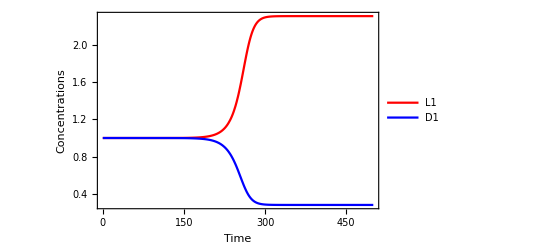

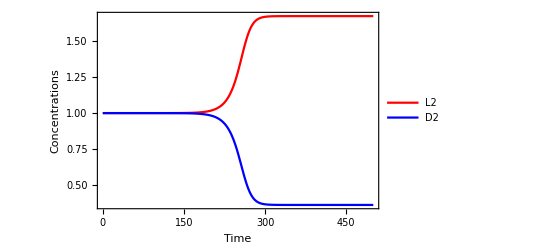

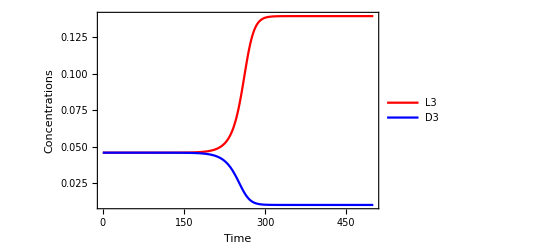

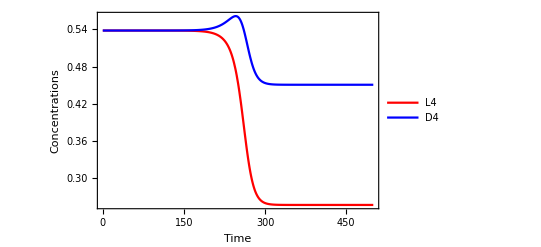

```mathematica
simulationTimeMin=0; 
simulationTimeMax=500; (*feel free to change*)
graficss=ReactionSystemSimulator[reactions,rates, Join[samplesList[[sampleNumber]],initialValues],0.000001,t,simulationTimeMin,simulationTimeMax];
```

SACNA also allows to export a simulation results to ChemKinLator simulator files with the function ExportToChemKinLator.

```mathematica
content=ExportToChemKinLator[reactions,rates, samplesList[[sampleNumber]],1/1000000000000000,1/1000000000000000,0,simulationTimeMax,1000];
```

Export::chtype: First argument $Canceled is not a valid file specification.

We could try to do the same with the second and third Routh-Hurwitz condition, but in this case it could take a lot of time.

The user would like to know which rate constant corresponds to some reactions. It can be done with the function GetReactionsAndRates.

```mathematica
GetReactionsAndRates[reactions,rates] //MatrixForm
```

(L1->L2 | k1
L2->L1 | k2
L1+L2->L3 | k3
L3->L1+L2 | k4
D2+L1->D4 | k5
D4->D2+L1 | k6
L3->2L1 | k7
2L1->L3 | k8
L4->D1+L1 | k9
D1+L1->L4 | k10
L4->D3 | k11
D3->L4 | k12
D1->D2 | k1
D2->D1 | k2
D1+D2->D3 | k3
D3->D1+D2 | k4
D1+L2->L4 | k5
L4->D1+L2 | k6
D3->2D1 | k7
2D1->D3 | k8
D4->D1+L1 | k9
D1+L1->D4 | k10
D4->L3 | k11
L3->D4 | k12)